{{0.,-75.},{1.,141.},{6.,269.},{16.,485.},{24.,525.},{25.,453.},{26.,-27.},{22.,-211.},{3.,-379.},{0.,-75.}}

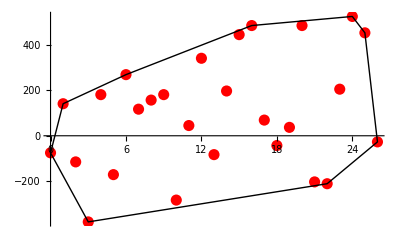

```mathematica
points=ReadList["C:\\Users\\User\\Desktop\\Новая папка\\проги\\5 семестр\\работы\\convex_hull\\points.txt",Real];
hulll=ReadList["C:\\Users\\User\\Desktop\\Новая папка\\проги\\5 семестр\\работы\\convex_hull\\hull.txt",Real];
partpoints=Partition[points,2];
parthull=Partition[hulll,2];
parthull=Insert[parthull,parthull[[1]],-1]
Show[{ListPlot[partpoints,PlotStyle->{PointSize[0.02],Red}],Graphics[Line[parthull]]}]
```